# Stably Wick Relaxing

## Initialisation

```mathematica
ClearAll["Global`*"]
```

## Introduction

### The problem

Wick relaxation gives a good (and often, fast) convergence to the ground-state, though Wick rotation yields a non-unitary Schrodinger equation; solutions break normalisation and rush to zero. Normalising once (at the end) causes precision problems in the numerical integration, and can cause numerical instability within the simulation.

### The solution

Normalisation should occur at every time-step, or some regular interval. I want to avoid coding my own numerical method; I’ll re-simulate until energy convergence is achieved

```mathematica
relaxWavefunction::usage = 
	"Relaxes a given wavefunction in a given potential (both interpolated or analytic), returning full evolution";

relaxWavefunction[psi_, potential_, {x_, xL_, xR_}, duration_] :=
	NDSolveValue[
		{
			-Derivative[0,1][ψ][x, t] ==  -Derivative[2,0][ψ][x, t] / 2 + ψ[x, t] potential,
			ψ[x, 0] == psi,
			ψ[xL, t] == 0,
			ψ[xR, t] == 0
		},
		ψ, {x, xL, xR}, {t, 0, duration}
	]
```

```mathematica
initialWavefunction::usage =
	"Returns a flat, analytic, initial wavefunction for wick relaxation";

initialWavefunction[{x_, xL_, xR_}] :=
	normaliseWavefunction[
		UnitStep[x - (xL+0.01)] - UnitStep[x - (xR-0.01)],
		{x, xL, xR}
	]
	
normaliseWavefunction[psi_, domain_:{x, -∞, ∞}] :=
	psi / Sqrt[NIntegrate[
		Abs[psi]^2,
		domain,
		Method -> {Automatic, "SymbolicProcessing" -> 0}
	]]
```

```mathematica
hamiltonian[psi_, potential_, r_:x] := 
	-1/2 D[psi, {r,2}] + potential psi
	
expectedEnergy[psi_, potential_,  domain_:{x, -∞, ∞}] :=
	With[
		{r = domain[[1]]},
		NIntegrate[
			(Conjugate[psi] /. Conjugate[r] -> r)
			(hamiltonian[psi, potential, r]),
			domain,
			Method->{Automatic, "SymbolicProcessing" ->0}
		]
	]


getGroundstate::usage = 
	"Returns the groundstate of a given potential (analytic or interpolated), found through Wick 
	relaxation by repeatedly performing NDSolve for duration timestep until TraditionalForm`";

getGroundstate[potential_, domain_:{x, -5, 5}, timestep_:0.1, threshold_:0.01] :=
	Module[
		{x, psi, prevE, curE},
		x = domain[[1]];
		psi = initialWavefunction[domain];
		prevE = expectedEnergy[psi, potential, domain];
		
		psi = Evaluate[relaxWavefunction[psi, potential, domain, timestep][x, timestep]];
		psi = normaliseWavefunction[psi, domain];
		curE = expectedEnergy[psi, potential, domain];
		
		While[
			Abs[(curE - prevE)/(curE timestep)] > threshold,
			prevE = curE;
			psi = Evaluate[relaxWavefunction[psi, potential, domain, timestep][x, timestep]];
			psi = normaliseWavefunction[psi, domain];
			curE = expectedEnergy[psi, potential, domain];
		];
		
		psi
	]
	
(* Evaluate suggestion from here: 
	https://mathematica.stackexchange.com/questions/29812/interpolating-function-inside-of-ndsolve *)
	
(* possible fix (interpolate back to table back to interpolate) here:
https://mathematica.stackexchange.com/questions/56964/problem-when-defining-function-through-nintegrate-and-ndsolve-and-interpolation 
*)
```

```mathematica
getGroundstate[1/2 x^2]
```

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

1.06 InterpolatingFunction[{{-5., 5.}, {0., 0.01}}, <>][x,0.01]

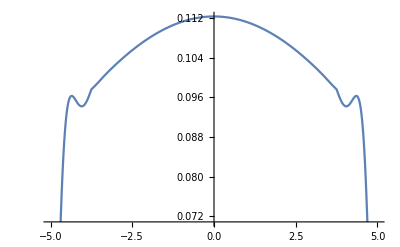

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

1.0378 InterpolatingFunction[{{-5., 5.}, {0., 0.01}}, <>][x,0.01]

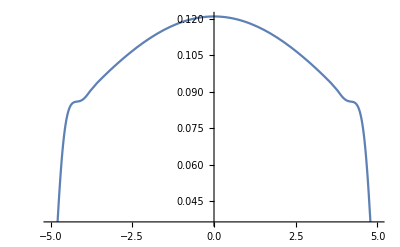

-Graphics-

```mathematica
normaliseWavefunction[relaxWavefunction[initialWavefunction[{x, -5, 5}], 1/2 x^2, {x, -5, 5}, 0.01][x, 0.01], {x, -5, 5}]
Plot[Abs[%]^2, {x, -5, 5}]

normaliseWavefunction[relaxWavefunction[%%, 1/2 x^2, {x, -5, 5}, 0.01][x, 0.01], {x, -5, 5}]
Plot[Abs[%]^2, {x, -5, 5}]
```